## Figure 1 (With charge)

```mathematica
(*rh represents horizon*)
```

```mathematica
Roots[r^4-2 M r+Q^2==0,r][[4,2]]
```

1/2 √((2 2^(2/3) Q^2)/(3^(1/3) (9 M^2+√3 √(27 M^4-16 Q^6))^(1/3))+(2^(1/3) (9 M^2+√3 √(27 M^4-16 Q^6))^(1/3))/3^(2/3))+1/2 √(-(2 2^(2/3) Q^2)/(3^(1/3) (9 M^2+√3 √(27 M^4-16 Q^6))^(1/3))-(2^(1/3) (9 M^2+√3 √(27 M^4-16 Q^6))^(1/3))/3^(2/3)+(4 M)/(√((2 2^(2/3) Q^2)/(3^(1/3) (9 M^2+√3 √(27 M^4-16 Q^6))^(1/3))+(2^(1/3) (9 M^2+√3 √(27 M^4-16 Q^6))^(1/3))/3^(2/3))))

(4 #1^3-2 #2)/#1^2-(2 (#1^4-2 #1 #2+#3^2))/#1^3&

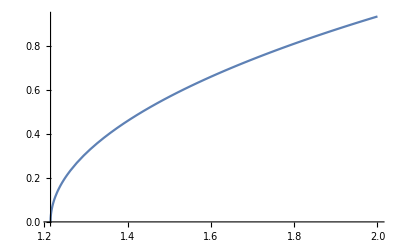

```mathematica
f[r_,M_,Q_,k_]:=k+1/r^2(r^4-2 M r+Q^2)
f1=Derivative[1,0,0,0][f]
Eta[r0_?NumericQ,r1_?NumberQ,M_,Q_,k_]:=NIntegrate[1/Sqrt[f[r,M,Q,k]],{r,r0,r1}]
rh[M_,Q_]:=Roots[r^4-2 M r+Q^2==0,r][[4,2]]//N
Plot[Eta[rh[1,0.5],r1,1,0.5,0],{r1,rh[1,0.5],2}]
```

```mathematica
Eta[rh[1,0.5],1.3,1,0.5,0]
```

0.310817

```mathematica
h[1.3,1,0.5,0]
```

4.09082

```mathematica
f1[r,M,Q,k]
```

(-2 M+4 r^3)/r^2-(2 (Q^2-2 M r+r^4))/r^3

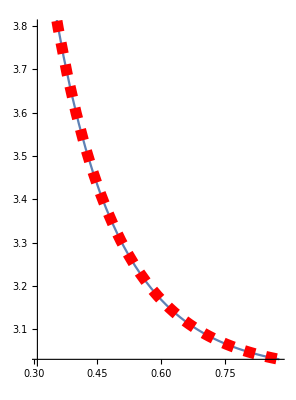

```mathematica
h[r_,M_,Q_,k_]:=Sqrt[f[r,M,Q,k]](f1[r,M,Q,k]r^4+4f[r,M,Q,k]r^3)/(2f[r,M,Q,k]r^4)
rh[M_,Q_]:=Roots[r^4-2 M r+Q^2==0,r][[4,2]]//N
Show[{ParametricPlot[{Eta[rh[1,0],r1,1,0,0],h[r1,1,0,0]},{r1,1.35,2}],ParametricPlot[{Eta[rh[1,0],r1,1,0,0],3 Coth[3Eta[rh[1,0],r1,1,0,0]]},{r1,1.26,2},PlotStyle->{Red,Dashing[0.02],Thickness[0.02]}]}]
```

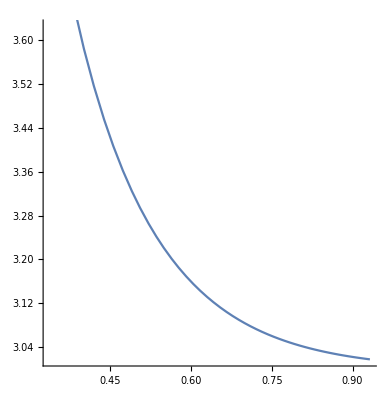

```mathematica
ParametricPlot[{Eta[rh[1,0.5],r1,1,0.5,0],h[r1,1,0.5,0]},{r1,rh[1,0.5]+.1,2}]
```

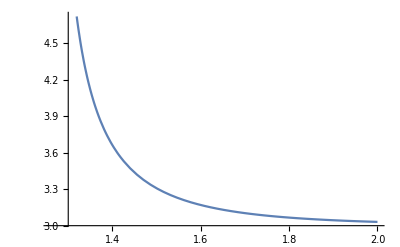

```mathematica
Plot[h[r1,1,0,0],{r1,rh[1,0],2}]
```

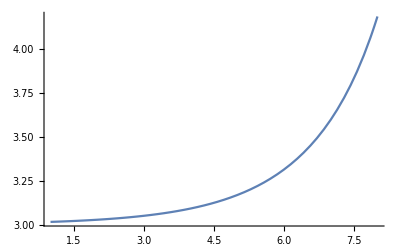

```mathematica
Plot[3 Coth[3 0.1 (11-x)],{x,1,8}]
```

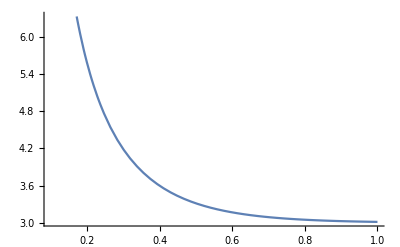

```mathematica
Plot[3 Coth[3x],{x,.1,1}]
```